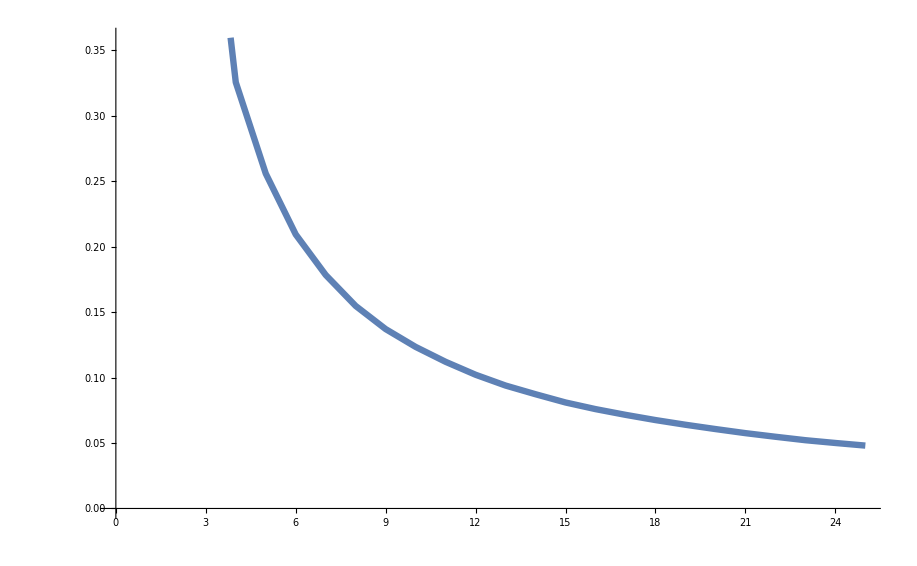

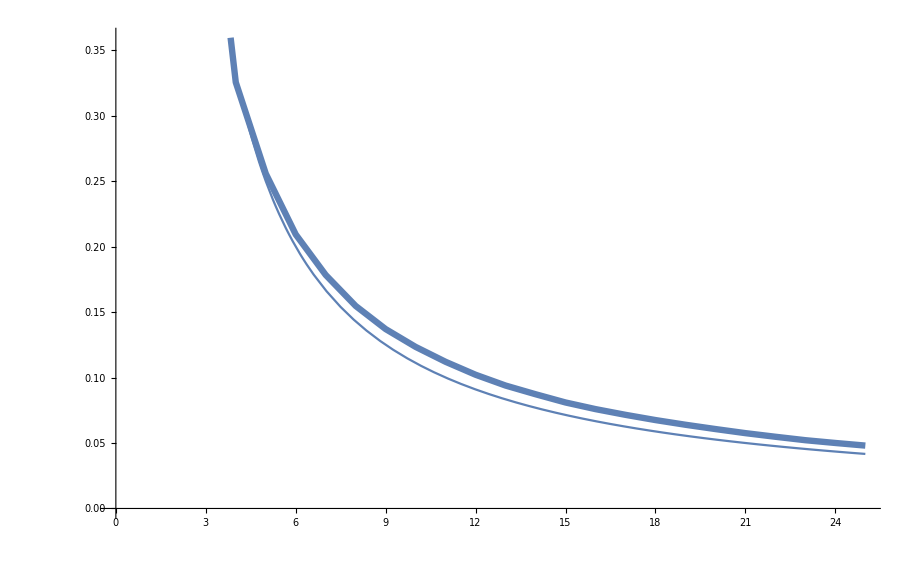

```mathematica
(*dataA10 = {0.069028, 0.123394, 0.103740, 0.102514, 0.101329, 0.101153, 0.102543,0.104086,  0.122916, 0.069298};
dataB10 = {0.069493, 0.123127, 0.103624, 0.102474, 0.100929, 0.101875, 0.102196, 0.103620, 0.123409, 0.069252};*)
data = {{3, 0.523138}, {4, 0.325476}, {5, 0.255773}, {6, 0.209290}, {7, 0.178337}, {8, 0.154669}, {9, 0.136995}, {10, 0.123394}, {11, 0.112002}, {12, 0.102123}, {13, 0.093879}, {14, 0.087246}, {15, 0.080949}, {16, 0.075884}, {17, 0.071516}, {18, 0.067519}, {19, 0.063942}, {20, 0.060655}, {21, 0.057538}, {22, 0.054773}, {23, 0.052145}, {24, 0.050022}, {25, 0.048030}};
xx = ListPlot[data, Joined -> True, PlotStyle -> {Thickness[0.005], Thickness[0.005]}, AxesStyle -> {Directive[Black, 22], Directive[Black, 22]}]
yy = Plot[1/(x - 1), {x, 3, 25}];
Show[xx, yy]
```